# Graph Learning

## Synthetic Data

We will make a Barabasi-Albert graph to define signals on.

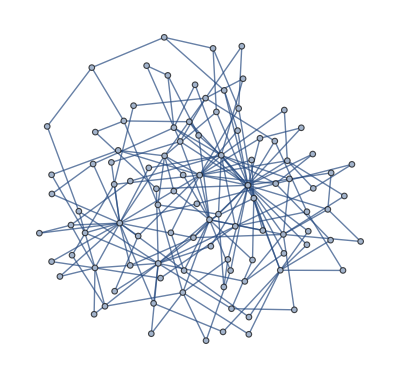

```mathematica
nVertices = 100;
k = 2;
degreeDist := BarabasiAlbertGraphDistribution[nVertices, k];
G = RandomGraph[degreeDist]
```

The goal of our project is to distinguish graph signals generated by two separate processes. To test the neural net, we can generate a bunch of graphs from two different processes, and compare them!

```mathematica
triangles[G_]:=triangles[G] =  Module[
{T= {}},
Do[Do[Do[
If[EdgeQ[G, i <-> j] && EdgeQ[G, j <-> k] && EdgeQ[G, k <-> i],
AppendTo[T, {i, j, k}]],
{k, 1, j}], {j, 1, i}], {i, 1, G // VertexCount}];
T];

processA[G_] :=Module[
{x = Table[0, {i, G // VertexCount}],
t = triangles[G], i, j, k, n, r},
Do[
{i, j, k} = t[[n]];
If[Random[] ≤ 1/2, 
r = RandomVariate[ExponentialDistribution[1]],
r = 0];
x[[i]] += r;
x[[j]] += r;
x[[k]] += r,
{n, 1, t // Length}];
x];
```

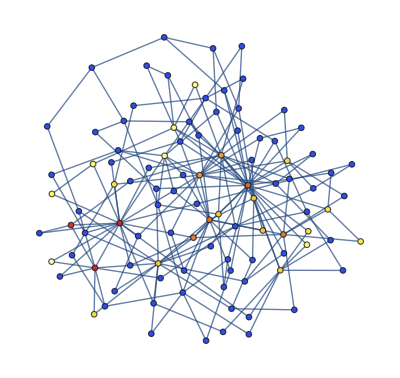

```mathematica
x = processA[G];
ColorFN = ColorData["TemperatureMap"];
colors = Table[v -> ColorFN[(x[[v]]/Max[x])^(1/8)], {v, G // VertexCount}];
Graph[G, VertexStyle -> colors]
```

```mathematica
processB[G_] := Table[
RandomVariate[ExponentialDistribution[1/(VertexDegree[G][[i]])]],
{i, G // VertexCount}];
```

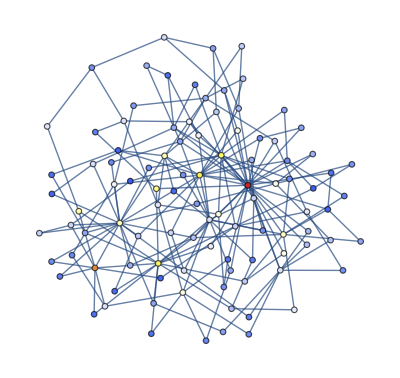

```mathematica
x = processB[G];
ColorFN = ColorData["TemperatureMap"];
colors = Table[v -> ColorFN[(x[[v]]/Max[x])^(1/2)], {v, G // VertexCount}];
Graph[G, VertexStyle -> colors]
```

```mathematica
procASignals = Table[processA[G], {i, 10000}];
procBSignals = Table[processB[G], {i, 10000}];
```

```mathematica
n = NormalizedLaplacianMatrix[G] // N;
```

```mathematica
dir = "C:\\Users\\Kevin Smith\\Desktop\\Network Science\\research\\data\\cases\\";
Export[dir <> "fullLaplacian.csv", n];
Export[dir <> "procASignals.csv", procASignals];
Export[dir <> "procBSignals.csv", procBSignals];
```

## Graph Partitioning

```mathematica
LaplacianMatrix[G_] := DiagonalMatrix[VertexDegree[G]]- AdjacencyMatrix[G];

NormalizedLaplacianMatrix[G_] :=Module[
{degrees = VertexDegree[G],
L = LaplacianMatrix[G],
pos, degMatrix},
pos = Table[Max[degrees[[i]], 1],{i, G // VertexCount}];
degMatrix = MatrixPower[DiagonalMatrix[pos], -1/2];
degMatrix.L.degMatrix];
```

```mathematica
SpectralPartition[G_]:= Module[
{L = NormalizedLaplacianMatrix[G], v},
v = Eigenvectors[-N@L, 2] // First // N;
# > 0& /@ v];
```

```mathematica
GraphBisect[G_, minSize_] := Module[{p, v1, v2, G1, G2},
If[Length[VertexList[G]] ≤ minSize,
{G},
p = SpectralPartition[G];
v1 = VertexList[G][[Position[p, True] // Flatten]];
v2 = VertexList[G][[Position[p, False] // Flatten]];
G1 = Subgraph[G, v1];
G2 = Subgraph[G, v2];
GraphBisect[G1, minSize]~Join~GraphBisect[G2, minSize]
]];
```

```mathematica
GraphPartition[G_, minSize_] := Module[
{subgraphs = GraphBisect[G, minSize],subgraphEnum},
subgraphEnum = Table[i, {i, Length[subgraphs]}];
Table[
Select[subgraphEnum, VertexQ[subgraphs[[#]], v]&],
{v, G // VertexList // Length}] // Flatten];
```

```mathematica
p = GraphPartition[G, 20]
```

{6,12,13,14,10,15,7,1,10,8,2,9,3,4,10,16,17,10,5,9,5,5,18,10,5,5,12,5,19,5,20,5,21,9,22,23,5,9,24,25,9,26,9,9,9,27,5,27,27,27,5,5,27,27,5,9,27,10,5,5,9,9,10,10,27,10,10,27,9,10,5,9,27,10,5,10,27,10,9,10,27,27,9,12,27,27,11,5,27,9,27,9,5,27,9,9,9,5,27,27}

```mathematica
ColorFN = ColorData["BrightBands"];
style = Table[v -> ColorFN[(p[[v]] - 1)/(Max[p] - 1)], {v, VertexCount[G]}];
```

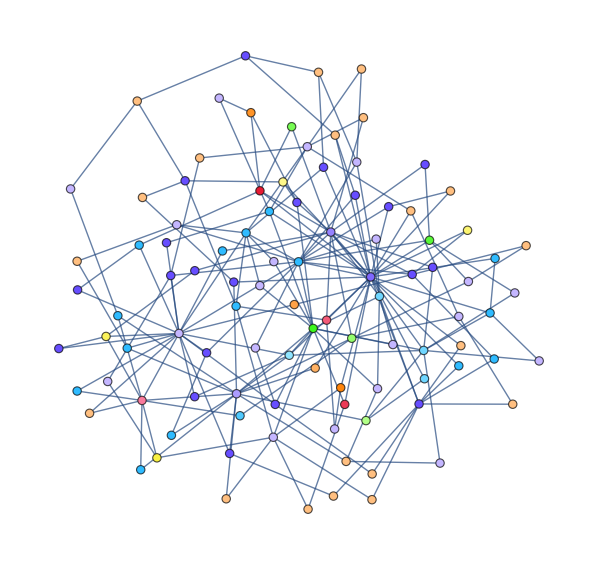

```mathematica
Graph[G, VertexStyle -> style]
```

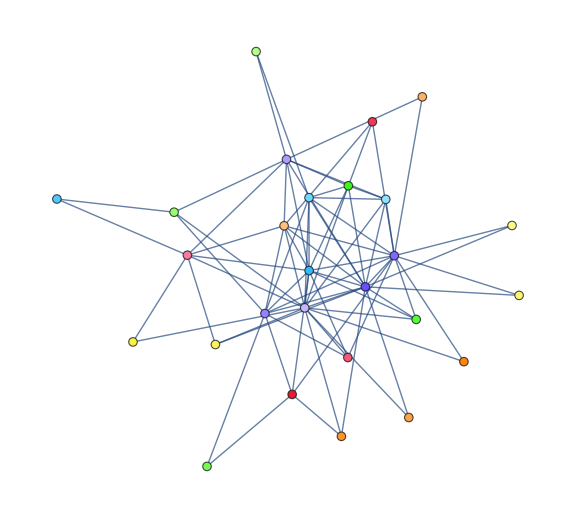

```mathematica
coarseGraph = SimpleGraph[p[[# // First]]<-> p[[# // Last]]& /@ EdgeList[G], 
VertexStyle -> Table[v -> ColorFN[(v - 1)/(Max[p] - 1)], {v, Max[p]}]]
```

```mathematica
dir = "C:\\Users\\Kevin Smith\\Desktop\\Network Science\\research\\data\\cases\\";
Export[dir <> "coarseLaplacian.csv", NormalizedLaplacianMatrix[coarseGraph] // N];
```